```mathematica
tF={FontFamily->"Times",FontSize->16};f1=Plot3D[{2x^2+3y^2,4x+6y-5},{x,-12,14},{y,-12,14},
Boxed->False,
Mesh->10,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
PlotStyle->{Opacity[0.6]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{{PointSize[Large],Point[{1,1,5}]},
Text[Style["(1,1,5)",tF],{1,1,200}]
}];
Show[f1,f2]
```

-Graphics3D-

```mathematica
tF={FontFamily->"Times",FontSize->16};f1=Plot3D[{2x^2+3y^2,4x+6y-5},{x,-5,7},{y,-5,7},
Boxed->False,
Mesh->10,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
PlotStyle->{Opacity[0.6]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{{PointSize[Large],Point[{1,1,5}]},
Text[Style["(1,1,5)",tF],{1,1,50}]
}];
Show[f1,f2]
```

-Graphics3D-

```mathematica
tF={FontFamily->"Times",FontSize->16};f1=Plot3D[{2x^2+3y^2,4x+6y-5},{x,-1,3},{y,-1,3},
Boxed->False,
Mesh->10,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
PlotStyle->{Opacity[0.6]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{{PointSize[Large],Point[{1,1,5}]},
Text[Style["(1,1,5)",tF],{1,1,15}]
}];
Show[f1,f2]
```

-Graphics3D-

```mathematica
tF={FontFamily->"Times",FontSize->16};f1=Plot3D[{2x^2+3y^2,4x+6y-5},{x,0.5,1.5},{y,0.5,1.5},
Boxed->False,
Mesh->10,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
PlotStyle->{Opacity[0.6]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{{PointSize[Large],Point[{1,1,5}]},
Text[Style["(1,1,5)",tF],{1,1,7}]
}];
Show[f1,f2]
```

-Graphics3D-

```mathematica
tF={FontFamily->"Times",FontSize->16};f1=Plot3D[{x*y/(x^2+y^2),0},{x,-1,1},{y,-1,1},
Boxed->False,
Mesh->10,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
PlotStyle->{Opacity[0.7]},
BoundaryStyle->None,
PlotPoints->40,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{{PointSize[Large],Point[{0,0,0}]},
Text[Style["0",tF],{0.1,-0.1,0}]
}];
Show[f1,f2]
```

-Graphics3D-

```mathematica
tF={FontFamily->"Times",FontSize->16};f1=Plot3D[{x*y/(x^2+y^2),0},{x,-1,1},{y,-1,1},
Boxed->False,
Mesh->10,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
PlotStyle->{Opacity[0.7]},
BoundaryStyle->None,
PlotPoints->40,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{{PointSize[Large],Point[{0,0,0}]},
Text[Style["0",tF],{0.1,-0.1,0}]
}];
Show[f1,f2]
```

-Graphics3D-

```mathematica
Plot3D[-Sqrt[x^2+y^2],{x,-1,1},{y,-1,1},
AspectRatio->Automatic,
Boxed->False,Axes->False,
Mesh->10,MeshFunctions->{#3&},MeshStyle->{White,Opacity[0.5]},
RegionFunction->Function[{x,y,z},x^2+y^2<1],
PlotPoints->50,
PlotStyle->{Opacity[0.8]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
]
```

-Graphics3D-

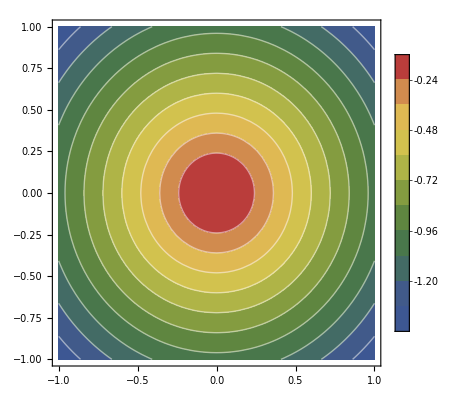

```mathematica
ContourPlot[-Sqrt[x^2+y^2],{x,-1,1},{y,-1,1},PlotLegends->Automatic,
ColorFunction->"DarkRainbow",ContourStyle->{White},Contours->10]
```

```mathematica
Plot3D[x*y*E^(-x^2-y^2),{x,-2.5,2.5},{y,-2.5,2.5},
AspectRatio->Automatic,
Boxed->False,Axes->False,
PlotRange->All,
Mesh->20,MeshFunctions->{#3&},MeshStyle->{White,Opacity[0.5]},
PlotPoints->50,
PlotStyle->{Opacity[0.8]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
]
```

-Graphics3D-

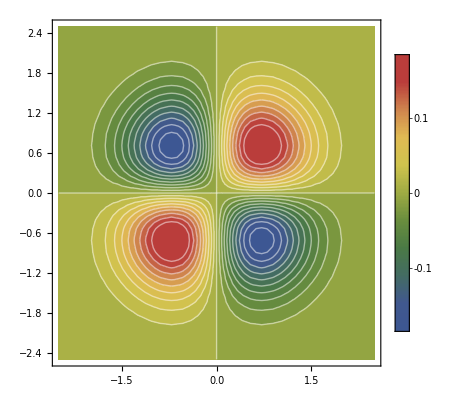

```mathematica
ContourPlot[x*y*E^(-x^2-y^2),{x,-2.5,2.5},{y,-2.5,2.5},PlotLegends->Automatic,
ColorFunction->"DarkRainbow",ContourStyle->{White},Contours->20]
```

```mathematica
f1=Plot3D[x^2-y^2,{x,-4,4},{y,-4,4},
AspectRatio->Automatic,
Boxed->False,Axes->False,
PlotRange->All,
Mesh->20,MeshFunctions->{#3&},MeshStyle->{White,Opacity[0.5]},
PlotPoints->50,
PlotStyle->{Opacity[0.8]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
];
f2=Graphics3D[{
{PointSize[Large],Point[{0,0,0}]},
{Arrowheads[0.02],Arrow[{{1,1,15},{0,0,0}}]},
Text[Style["鞍点",tF,Blue,Italic],{1,1,17}]
}];
Show[f1,f2]
```

-Graphics3D-

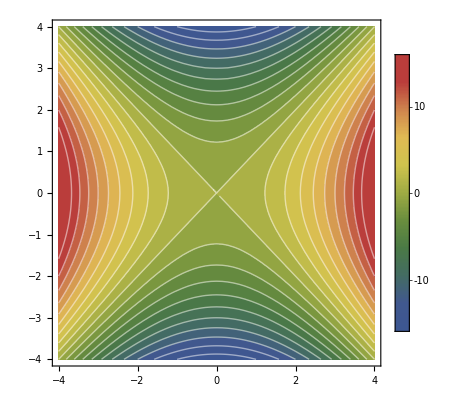

```mathematica
ContourPlot[x^2-y^2,{x,-4,4},{y,-4,4},PlotLegends->Automatic,
ColorFunction->"DarkRainbow",ContourStyle->{White},Contours->20]
```